```mathematica
Clear["Global`*"];
```

# Aβ42

## Import data for 1μM Aβ42 with increasing inhibitor concentration

#### Normalised data (normalised using amylofit)

```mathematica
SetDirectory[NotebookDirectory[]]
data0=Import["Input_files/AB42_1_0D/datadot.tsv"];
data0=Delete[data0,1];
data1=Import["Input_files/AB42_1_1D/datadot.tsv"];
data1=Delete[data1,1];
data2=Import["Input_files/AB42_1_2D/datadot.tsv"];
data2=Delete[data2,1];
data6=Import["Input_files/AB42_1_6D/datadot.tsv"];
data6=Delete[data6,1];
data10=Import["Input_files/AB42_1_10D/datadot.tsv"];
data10=Delete[data10,1];
data15=Import["Input_files/AB42_1_15D/datadot.tsv"];
data15=Delete[data15,1];
data20=Import["Input_files/AB42_1_20D/datadot.tsv"];
data20=Delete[data20,1];
```

/Users/gabiheller/Desktop/Heller_10074_G5_data_code/ThT_aggregation/Kinetic modelling

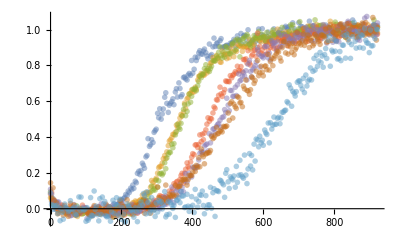

```mathematica
dataplot=ListPlot[{data0,data1,data2,data6,data10,data15,data20},PlotMarkers->{•,6},PlotStyle->Opacity[0.5]]
```

#### Unnormalised data

```mathematica
rawdata0=Import["Input_files/AB42_raw_data/data.tsv",{"Data",All,{1,2}}];
rawdata0=Delete[rawdata0,1];
rawdata1=Import["Input_files/AB42_raw_data/data.tsv",{"Data",All,{3,4}}];
rawdata1=Delete[rawdata1,1];
rawdata2=Import["Input_files/AB42_raw_data/data.tsv",{"Data",All,{5,6}}];
rawdata2=Delete[rawdata2,1];
rawdata6=Import["Input_files/AB42_raw_data/data.tsv",{"Data",All,{7,8}}];
rawdata6=Delete[rawdata6,1];
rawdata10=Import["Input_files/AB42_raw_data/data.tsv",{"Data",All,{9,10}}];
rawdata10=Delete[rawdata10,1];
rawdata15=Import["Input_files/AB42_raw_data/data.tsv",{"Data",All,{11,12}}];
rawdata15=Delete[rawdata15,1];
rawdata20=Import["Input_files/AB42_raw_data/data.tsv",{"Data",All,{13,14}}];
rawdata20=Delete[rawdata20,1];
```

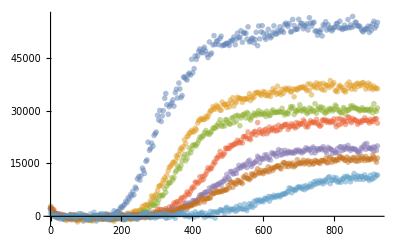

```mathematica
rawdataplotshort2=ListPlot[{rawdata0,rawdata1,rawdata2,rawdata6,rawdata10,rawdata15,rawdata20},PlotMarkers->{•,6},PlotStyle->Opacity[0.5]]
```

#### Normalization factors (from amylofit):

```mathematica
lmax=Length[rawdata0]-1;
l=67;
norm0=1/(l+1)*Sum[rawdata0[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata1]-1;
l=41;
norm1=1/(l+1)*Sum[rawdata1[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata2]-1;
l=61;
norm2=1/(l+1)*Sum[rawdata2[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata6]-1;
l=22;
norm6=1/(l+1)*Sum[rawdata6[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata10]-1;
l=31;
norm10=1/(l+1)*Sum[rawdata10[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata15]-1;
l=10;
norm15=1/(l+1)*Sum[rawdata15[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata20];
l=1;
norm20=1/(l+1)*Sum[rawdata20[[n]][[2]],{n,lmax-l,lmax}]
```

53832.9

36828.5

30274.7

27125.2

19238.7

16305.7

11673.5

## Monomer sequestration model (equilibrium dot-blot data)

```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

FittedModel[92.7 (1+0.14917 x)]

FittedModel[92.7 (1+0.144899 x)]

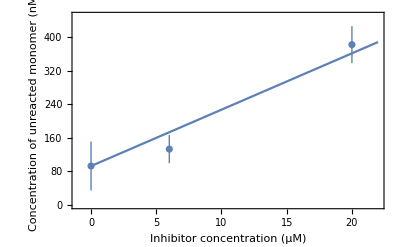

| Estimate | Standard Error | t-Statistic | P-Value
k2 | 6.90137 | 0.957415 | 7.20834 | 0.0187072

```mathematica
Clear[k2,x]
listerr={{{0,92.7636},ErrorBar[58.30915]},{{6,133.0446},ErrorBar[33.57284]},{{20,382.0477},ErrorBar[43.96399]}};

list={{0,92.7636},{6,133.0446},{20,382.0477}};
errors={58.30915,33.57284,43.96399};

nlm=NonlinearModelFit[list,(1+x/k2)*92.7,k2,x]

nlm=NonlinearModelFit[list,(1+x/k2)*92.7,k2,x,Weights->1/errors^2]

Show[ErrorListPlot[listerr,PlotRange->{{-1,22},{0,450}},PlotStyle->{Thick,Thick},Frame->True,FrameStyle->Black,FrameLabel->{"Inhibitor concentration (μM)","Concentration of unreacted monomer (nM)"}],Plot[nlm[x],{x,0,22}]]

nlm["ParameterTable"]
```

## Global fit of Aβ42 data

#### Global fit: preparation of data as a single dataset

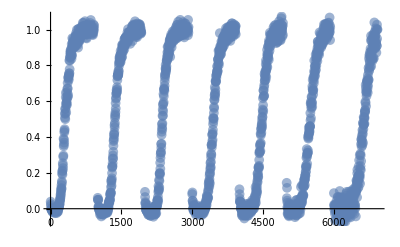

```mathematica
data={};
For[i=0,i<Length[data0],i++,
data=Append[data,{data0[[i+1,1]],data0[[i+1,2]]}]
]

For[i=0,i<Length[data1],i++,
data=Append[data,{data1[[i+1,1]]+1000,data1[[i+1,2]]}]
]

For[i=0,i<Length[data2],i++,
data=Append[data,{data2[[i+1,1]]+2000,data2[[i+1,2]]}]
]

For[i=0,i<Length[data6],i++,
data=Append[data,{data6[[i+1,1]]+3000,data6[[i+1,2]]}]
]

For[i=0,i<Length[data10],i++,
data=Append[data,{data10[[i+1,1]]+4000,data10[[i+1,2]]}]
]

For[i=0,i<Length[data15],i++,
data=Append[data,{data15[[i+1,1]]+5000,data15[[i+1,2]]}]
]

For[i=0,i<Length[data20],i++,
data=Append[data,{data20[[i+1,1]]+6000,data20[[i+1,2]]}]
]



dataplottot=ListPlot[{data},PlotMarkers->{Automatic,10},PlotStyle->Opacity[0.6]]
```

#### Perform the global fit

General::munfl: Exp[-710.3] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
Keq | 0.024975 | 0.00054831 | 45.5492 | 3.31699×10^-309

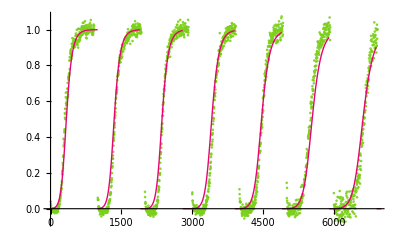

```mathematica
Clear[Keq]
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;
k2=5.9*10^(10)*3600/kp;
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];
theta=2/(2*3);

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)
i01=1.;
i02=2.;
i06=6.;
i010=10.;
i015=15.;
i020=20.;

(*Mass formula*)

Mass[t_,lambda_,kappa_]:=1-(((((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]+Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2))/(((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]+Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2)Exp[kappa*t]))*((((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]-Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2)Exp[kappa*t])/(((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]-Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2))))^(kappa*(theta+(2/nc)*lambda^2/kappa^2)/(Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2]))*Exp[-kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]*t];

(* Fitting function *)

nlm=NonlinearModelFit[data,Piecewise[{{Mass[t,λ,κ],t<1000},{Mass[t-1000,λ*(1/(1+Abs[Keq]*i01))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i01))^((n2+1)/2)],1000≤t<1900},{Mass[t-2000,λ*(1/(1+Abs[Keq]*i02))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i02))^((n2+1)/2)],2000≤t<2800},{Mass[t-3000,λ*(1/(1+Abs[Keq]*i06))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i06))^((n2+1)/2)],3000≤t<3900},{Mass[t-4000,λ*(1/(1+Abs[Keq]*i010))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i010))^((n2+1)/2)],4000≤t<4900},{Mass[t-5000,λ*(1/(1+Abs[Keq]*i015))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i015))^((n2+1)/2)],5000≤t<5900},{Mass[t-6000,λ*(1/(1+Abs[Keq]*i020))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i020))^((n2+1)/2)],6000≤t<6900}}],{{Keq,0.04}},t];
(*Print fitting parameters*)
nlm["ParameterTable"]

Show[
ListPlot[{data},PlotStyle->{{RGBColor[.482,.816,.098],Opacity[0.9]}}],(*ploterr2um,*)Plot[{nlm[t]},{t,0,7000},PlotStyle->{{RGBColor[.9,.02,.45],Thick}},PlotRange->All]]
```

#### Calculation of the Kd as 1/Keq

```mathematica
1/0.024938099244083432
```

40.0993

#### Plot global fit

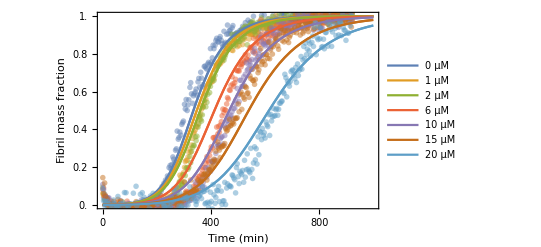

```mathematica
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)

Keq=0.024938099244083432; (*FROM GLOBAL FIT*)

i01=1.;
i02=2.;
i06=6.;
i010=10.;
i015=15.;
i020=20.;

(*Derived parameters*)
σ0=kofffibrils/kp*1/mtot*(1);
σ1=kofffibrils/kp*1/mtot*(1+Keq*i01);
ξ1=1/(1+Keq*i01);
σ2=kofffibrils/kp*1/mtot*(1+Keq*i02);
ξ2=1/(1+Keq*i02);
σ6=kofffibrils/kp*1/mtot*(1+Keq*i06);
ξ6=1/(1+Keq*i06);
σ10=kofffibrils/kp*1/mtot*(1+Keq*i010);
ξ10=1/(1+Keq*i010);
σ15=kofffibrils/kp*1/mtot*(1+Keq*i015);
ξ15=1/(1+Keq*i015);
σ20=kofffibrils/kp*1/mtot*(1+Keq*i020);
ξ20=1/(1+Keq*i020);


(*Plot solutions*)
Show[Plot[{Mass[t,λ,κ],Mass[t,λ*ξ1^((nc+1)/2),κ*ξ1^((n2+1)/2)],Mass[t,λ*ξ2^((nc+1)/2),κ*ξ2^((n2+1)/2)],Mass[t,λ*ξ6^((nc+1)/2),κ*ξ6^((n2+1)/2)],Mass[t,λ*ξ10^((nc+1)/2),κ*ξ10^((n2+1)/2)],Mass[t,λ*ξ15^((nc+1)/2),κ*ξ15^((n2+1)/2)],Mass[t,λ*ξ20^((nc+1)/2),κ*ξ20^((n2+1)/2)]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}},PlotLegends->LineLegend[{"0 μM","1 μM","2 μM","6 μM","10 μM","15 μM","20 μM"}]],dataplot,Plot[{Mass[t,λ,κ],Mass[t,λ*ξ1^((nc+1)/2),κ*ξ1^((n2+1)/2)],Mass[t,λ*ξ2^((nc+1)/2),κ*ξ2^((n2+1)/2)],Mass[t,λ*ξ6^((nc+1)/2),κ*ξ6^((n2+1)/2)],Mass[t,λ*ξ10^((nc+1)/2),κ*ξ10^((n2+1)/2)],Mass[t,λ*ξ15^((nc+1)/2),κ*ξ15^((n2+1)/2)],Mass[t,λ*ξ20^((nc+1)/2),κ*ξ20^((n2+1)/2)]},{t,0,1000},PlotRange->{All,{0,1}}]]
```

#### Export data as xls

```mathematica
m0=Table[{t,Mass[t,λ,κ],
Mass[t,λ*ξ1^((nc+1)/2),κ*ξ1^((n2+1)/2)],
Mass[t,λ*ξ2^((nc+1)/2),κ*ξ2^((n2+1)/2)],
Mass[t,λ*ξ6^((nc+1)/2),κ*ξ6^((n2+1)/2)],
Mass[t,λ*ξ10^((nc+1)/2),κ*ξ10^((n2+1)/2)],
Mass[t,λ*ξ15^((nc+1)/2),κ*ξ15^((n2+1)/2)],
Mass[t,λ*ξ20^((nc+1)/2),κ*ξ20^((n2+1)/2)]},{t,0,3000,1}];
m0//TableForm;

Export["Fit_Ab42_normalised.xls",m0,"XLS"]
```

Fit_Ab42_normalised.xls

#### Plot global fit on raw data

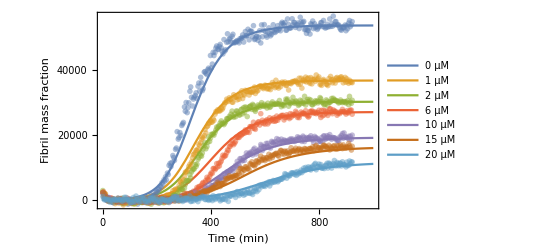

```mathematica
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)

Keq=1/(40*10^(-6)); (*FROM GLOBAL FIT*)

i01=1.*10^(-6);
i02=2.*10^(-6);
i06=6.*10^(-6);
i010=10.*10^(-6);
i015=15.*10^(-6);
i020=20.*10^(-6);
kon=1.5*10^(3)*60;
koff=kon/Keq;

(*Derived parameters*)
σ0=kofffibrils/kp*1/mtot*(1);
σ1=kofffibrils/kp*1/mtot*(1+Keq*i01);
ξ1=1/(1+Keq*i01);
σ2=kofffibrils/kp*1/mtot*(1+Keq*i02);
ξ2=1/(1+Keq*i02);
σ6=kofffibrils/kp*1/mtot*(1+Keq*i06);
ξ6=1/(1+Keq*i06);
σ10=kofffibrils/kp*1/mtot*(1+Keq*i010);
ξ10=1/(1+Keq*i010);
σ15=kofffibrils/kp*1/mtot*(1+Keq*i015);
ξ15=1/(1+Keq*i015);
σ20=kofffibrils/kp*1/mtot*(1+Keq*i020);
ξ20=1/(1+Keq*i020);


(*Plot solutions*)

Show[Plot[{norm0*Mass[t,λ,κ],
norm1*Mass[t,λ*ξ1^((nc+1)/2),κ*ξ1^((n2+1)/2)],
norm2*Mass[t,λ*ξ2^((nc+1)/2),κ*ξ2^((n2+1)/2)],
norm6*Mass[t,λ*ξ6^((nc+1)/2),κ*ξ6^((n2+1)/2)],
norm10*Mass[t,λ*ξ10^((nc+1)/2),κ*ξ10^((n2+1)/2)],
norm15*Mass[t,λ*ξ15^((nc+1)/2),κ*ξ15^((n2+1)/2)],
norm20*Mass[t,λ*ξ20^((nc+1)/2),κ*ξ20^((n2+1)/2)]},{t,0,1000},PlotRange->{All,All},PlotStyle->{Thick},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,80000,20000],None},{Range[0,1000,200],None}},PlotLegends->LineLegend[{"0 μM","1 μM","2 μM","6 μM","10 μM","15 μM","20 μM"}]],rawdataplotshort2]
```

#### Export data as xls

```mathematica
m0=Table[{t,norm0*Mass[t,λ,κ],
norm1*Mass[t,λ*ξ1^((nc+1)/2),κ*ξ1^((n2+1)/2)],
norm2*Mass[t,λ*ξ2^((nc+1)/2),κ*ξ2^((n2+1)/2)],
norm6*Mass[t,λ*ξ6^((nc+1)/2),κ*ξ6^((n2+1)/2)],
norm10*Mass[t,λ*ξ10^((nc+1)/2),κ*ξ10^((n2+1)/2)],
norm15*Mass[t,λ*ξ15^((nc+1)/2),κ*ξ15^((n2+1)/2)],
norm20*Mass[t,λ*ξ20^((nc+1)/2),κ*ξ20^((n2+1)/2)]},{t,0,3000,1}];
m0//TableForm;

Export["Fit_Ab42_raw.xls",m0,"XLS"]
```

Fit_Ab42_raw.xls

## Effective rates

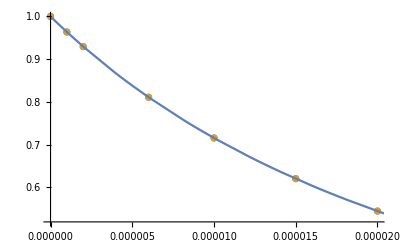

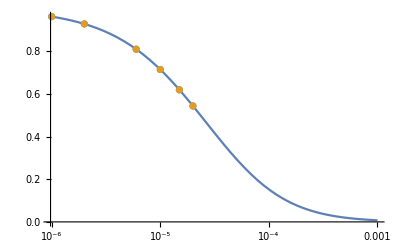

```mathematica
lambdaeffective={{0,1},{i01,ξ1^((nc+1)/2)},{i02,ξ2^((nc+1)/2)},{i06,ξ6^((nc+1)/2)},{i010,ξ10^((nc+1)/2)},{i015,ξ15^((nc+1)/2)},{i020,ξ20^((nc+1)/2)}};

kappaeffective={{0,1},{i01,ξ1^((n2+1)/2)},{i02,ξ2^((n2+1)/2)},{i06,ξ6^((n2+1)/2)},{i010,ξ10^((n2+1)/2)},{i015,ξ15^((n2+1)/2)},{i020,ξ20^((n2+1)/2)}};

Show[ListPlot[{lambdaeffective,kappaeffective}],Plot[1/(1+Keq*i)^((n2+1)/2),{i,0,200*10^(-6)}]]

Show[LogLinearPlot[1/(1+Keq*i)^((n2+1)/2),{i,0,1000*10^(-6)}],ListLogLinearPlot[{lambdaeffective,kappaeffective}]]
```

## Elongation data

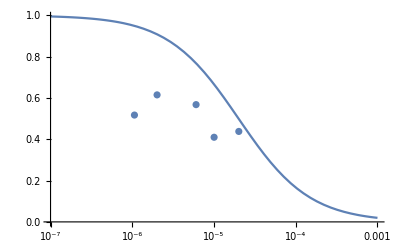

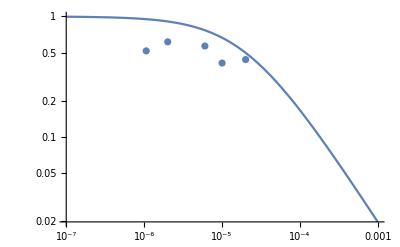

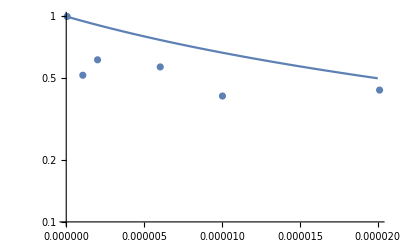

```mathematica
datael={{0.05747126436781613*10^(-6),1.0000000000000002},{
1.063218390804598*10^(-6),0.5174552914616355},{
2.0114942528735633*10^(-6),0.6152014367337444},{
6.034482758620689*10^(-6),0.5679828991002636},{
10.028735632183908*10^(-6),0.4099366644083613},{
20.114942528735632*10^(-6),0.43814564276036994}};

Kequi=1/(20*10^(-6));
Show[LogLinearPlot[1/(1+Kequi*i)^(2/2),{i,0.1*10^(-6),10^(-3)}],ListLogLinearPlot[datael]]
Show[LogLogPlot[1/(1+Kequi*i)^(2/2),{i,0.1*10^(-6),10^(-3)}],ListLogLogPlot[datael,PlotRange->{All,{0.1,1}}]]
Show[LogPlot[1/(1+Kequi*i)^(2/2),{i,0,20*10^(-6)},PlotRange->{{0,20*10^(-6)},{0.1,1}}],ListLogPlot[datael,PlotRange->{All,{0.01,1}}]]
```

## Misfit to inhibition of secondary nucleation (drug binding fibril surface)

#### Here perform the global fit just by varying kappa

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::munfl: Exp[-1205.39] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
Keq | 0.189047 | 0.00274721 | 68.8141 | 0.

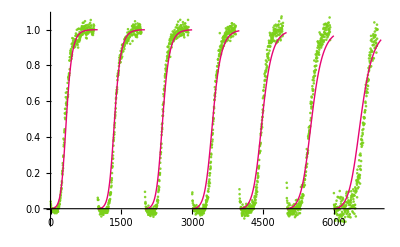

```mathematica
Clear[Keq]
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];
theta=2/(2*3);

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)
i01=1.;
i02=2.;
i06=6.;
i010=10.;
i015=15.;
i020=20.;

(*Mass formula*)

Mass[t_,lambda_,kappa_]:=1-(((((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]+Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2))/(((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]+Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2)Exp[kappa*t]))*((((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]-Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2)Exp[kappa*t])/(((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]-Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2))))^(kappa*(theta+(2/nc)*lambda^2/kappa^2)/(Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2]))*Exp[-kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]*t];

(* Fitting function *)

nlm=NonlinearModelFit[data,Piecewise[{{Mass[t,λ,κ],t<1000},{Mass[t-1000,λ,κ*(1/(1+Abs[Keq]*i01))^((1)/2)],1000≤t<2000},{Mass[t-2000,λ,κ*(1/(1+Abs[Keq]*i02))^((1)/2)],2000≤t<3000},{Mass[t-3000,λ,κ*(1/(1+Abs[Keq]*i06))^((1)/2)],3000≤t<4000},{Mass[t-4000,λ,κ*(1/(1+Abs[Keq]*i010))^((1)/2)],4000≤t<5000},{Mass[t-5000,λ,κ*(1/(1+Abs[Keq]*i015))^((1)/2)],5000≤t<6000},{Mass[t-6000,λ,κ*(1/(1+Abs[Keq]*i020))^((1)/2)],6000≤t<7000}}],{{Keq,0.01}},t];
(*Print fitting parameters*)
nlm["ParameterTable"]

Show[
ListPlot[{data},PlotStyle->{{RGBColor[.482,.816,.098],Opacity[0.9]}}],(*ploterr2um,*)Plot[{nlm[t]},{t,0,7000},PlotStyle->{{RGBColor[.9,.02,.45],Thick}},PlotRange->All]]
```

#### Plot global fit (normalised)

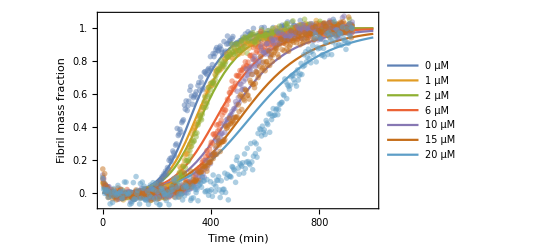

```mathematica
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)

Keq=0.18904673845825865; (*FROM GLOBAL FIT*)

i01=1.;
i02=2.;
i06=6.;
i010=10.;
i015=15.;
i020=20.;
kon=1.5*10^(3)*60;
koff=kon/Keq;

(*Derived parameters*)

ξ1=1/(1+Keq*i01);
ξ2=1/(1+Keq*i02);
ξ6=1/(1+Keq*i06);
ξ10=1/(1+Keq*i010);
ξ15=1/(1+Keq*i015);
ξ20=1/(1+Keq*i020);


(*Plot solutions*)

Show[Plot[{Mass[t,λ,κ],Mass[t,λ,κ*ξ1^((1)/2)],Mass[t,λ,κ*ξ2^((1)/2)],Mass[t,λ,κ*ξ6^((1)/2)],Mass[t,λ,κ*ξ10^((1)/2)],Mass[t,λ,κ*ξ15^((1)/2)],Mass[t,λ,κ*ξ20^((1)/2)]},{t,0,1000},PlotRange->{All,All},PlotStyle->{Thick},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}},PlotLegends->LineLegend[{"0 μM","1 μM","2 μM","6 μM","10 μM","15 μM","20 μM"}]],dataplot]
```

#### Plot on raw data

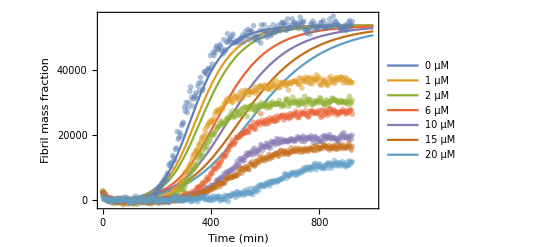

```mathematica
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)

Keq=0.18904673845825865; (*FROM GLOBAL FIT*)

i01=1.;
i02=2.;
i06=6.;
i010=10.;
i015=15.;
i020=20.;
kon=1.5*10^(3)*60;
koff=kon/Keq;

(*Derived parameters*)

ξ1=1/(1+Keq*i01);
ξ2=1/(1+Keq*i02);
ξ6=1/(1+Keq*i06);
ξ10=1/(1+Keq*i010);
ξ15=1/(1+Keq*i015);
ξ20=1/(1+Keq*i020);


(*Plot solutions*)

Show[Plot[{norm0*Mass[t,λ,κ],norm0*Mass[t,λ,κ*ξ1^((1)/2)],norm0*Mass[t,λ,κ*ξ2^((1)/2)],norm0*Mass[t,λ,κ*ξ6^((1)/2)],norm0*Mass[t,λ,κ*ξ10^((1)/2)],norm0*Mass[t,λ,κ*ξ15^((1)/2)],norm0*Mass[t,λ,κ*ξ20^((1)/2)]},{t,0,1000},PlotRange->{All,All},PlotStyle->{Thick},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,80000,20000],None},{Range[0,1000,200],None}},PlotLegends->LineLegend[{"0 μM","1 μM","2 μM","6 μM","10 μM","15 μM","20 μM"}]],rawdataplotshort2]
```

#### Export data as xls

```mathematica
m0=Table[{t,norm0*Mass[t,λ,κ],norm0*Mass[t,λ,κ*ξ1^((1)/2)],norm0*Mass[t,λ,κ*ξ2^((1)/2)],norm0*Mass[t,λ,κ*ξ6^((1)/2)],norm0*Mass[t,λ,κ*ξ10^((1)/2)],norm0*Mass[t,λ,κ*ξ15^((1)/2)],norm0*Mass[t,λ,κ*ξ20^((1)/2)]},{t,0,3000,1}];
m0//TableForm;

Export["MisFit_Ab42_2ndnuc_raw.xls",m0,"XLS"]
```

MisFit_Ab42_2ndnuc_raw.xls

## Misfit to inhibition of elongation (drug binding fibril ends)

#### Here perform the global fit

| Estimate | Standard Error | t-Statistic | P-Value
Keq | 0.107712 | 0.0031061 | 34.6775 | 1.08386×10^-205

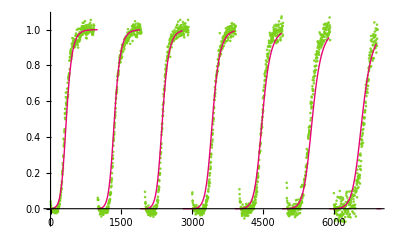

```mathematica
Clear[Keq]
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];
theta=2/(2*3);

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)
i01=1.;
i02=2.;
i06=6.;
i010=10.;
i015=15.;
i020=20.;

(*Mass formula*)

Mass[t_,lambda_,kappa_]:=1-(((((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]+Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2))/(((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]+Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2)Exp[kappa*t]))*((((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]-Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2)Exp[kappa*t])/(((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]-Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2))))^(kappa*(theta+(2/nc)*lambda^2/kappa^2)/(Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2]))*Exp[-kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]*t];

(* Fitting function *)

nlm=NonlinearModelFit[data,Piecewise[{{Mass[t,λ,κ],t<1000},{Mass[t-1000,λ*(1/(1+Abs[Keq]*i01))^((1)/2),κ*(1/(1+Abs[Keq]*i01))^((1)/2)],1000≤t<1900},{Mass[t-2000,λ*(1/(1+Abs[Keq]*i02))^((1)/2),κ*(1/(1+Abs[Keq]*i02))^((1)/2)],2000≤t<2800},{Mass[t-3000,λ*(1/(1+Abs[Keq]*i06))^((1)/2),κ*(1/(1+Abs[Keq]*i06))^((1)/2)],3000≤t<3900},{Mass[t-4000,λ*(1/(1+Abs[Keq]*i010))^((1)/2),κ*(1/(1+Abs[Keq]*i010))^((1)/2)],4000≤t<4900},{Mass[t-5000,λ*(1/(1+Abs[Keq]*i015))^((1)/2),κ*(1/(1+Abs[Keq]*i015))^((1)/2)],5000≤t<5900},{Mass[t-6000,λ*(1/(1+Abs[Keq]*i020))^((1)/2),κ*(1/(1+Abs[Keq]*i020))^((1)/2)],6000≤t<6900}}],{{Keq,0.04}},t];
(*Print fitting parameters*)
nlm["ParameterTable"]

Show[
ListPlot[{data},PlotStyle->{{RGBColor[.482,.816,.098],Opacity[0.9]}}],(*ploterr2um,*)Plot[{nlm[t]},{t,0,7000},PlotStyle->{{RGBColor[.9,.02,.45],Thick}},PlotRange->All]]
```

#### Plot global fit on normalised data

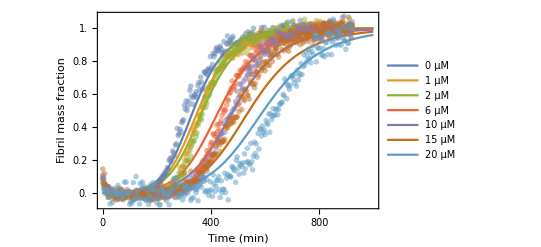

```mathematica
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)

Keq=0.10771204129773423; (*FROM GLOBAL FIT*)

i01=1.;
i02=2.;
i06=6.;
i010=10.;
i015=15.;
i020=20.;
kon=1.5*10^(3)*60;
koff=kon/Keq;

(*Derived parameters*)

ξ1=1/(1+Keq*i01);
ξ2=1/(1+Keq*i02);
ξ6=1/(1+Keq*i06);
ξ10=1/(1+Keq*i010);
ξ15=1/(1+Keq*i015);
ξ20=1/(1+Keq*i020);


(*Plot solutions*)

Show[Plot[{Mass[t,λ,κ],Mass[t,λ*ξ1^((1)/2),κ*ξ1^((1)/2)],Mass[t,λ*ξ2^((1)/2),κ*ξ2^((1)/2)],Mass[t,λ*ξ6^((1)/2),κ*ξ6^((1)/2)],Mass[t,λ*ξ10^((1)/2),κ*ξ10^((1)/2)],Mass[t,λ*ξ15^((1)/2),κ*ξ15^((1)/2)],Mass[t,λ*ξ20^((1)/2),κ*ξ20^((1)/2)]},{t,0,1000},PlotRange->{All,All},PlotStyle->{Thick},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}},PlotLegends->LineLegend[{"0 μM","1 μM","2 μM","6 μM","10 μM","15 μM","20 μM"}]],dataplot]
```

#### Plot global fit on raw data

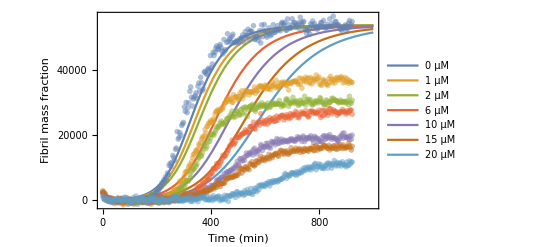

```mathematica
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)

Keq=0.10771204129773423; (*FROM GLOBAL FIT*)

i01=1.;
i02=2.;
i06=6.;
i010=10.;
i015=15.;
i020=20.;
kon=1.5*10^(3)*60;
koff=kon/Keq;

(*Derived parameters*)

ξ1=1/(1+Keq*i01);
ξ2=1/(1+Keq*i02);
ξ6=1/(1+Keq*i06);
ξ10=1/(1+Keq*i010);
ξ15=1/(1+Keq*i015);
ξ20=1/(1+Keq*i020);


(*Plot solutions*)

Show[Plot[{norm0*Mass[t,λ,κ],norm0*Mass[t,λ*ξ1^((1)/2),κ*ξ1^((1)/2)],norm0*Mass[t,λ*ξ2^((1)/2),κ*ξ2^((1)/2)],norm0*Mass[t,λ*ξ6^((1)/2),κ*ξ6^((1)/2)],norm0*Mass[t,λ*ξ10^((1)/2),κ*ξ10^((1)/2)],norm0*Mass[t,λ*ξ15^((1)/2),κ*ξ15^((1)/2)],norm0*Mass[t,λ*ξ20^((1)/2),κ*ξ20^((1)/2)]},{t,0,1000},PlotRange->{All,All},PlotStyle->{Thick},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,80000,20000],None},{Range[0,1000,200],None}},PlotLegends->LineLegend[{"0 μM","1 μM","2 μM","6 μM","10 μM","15 μM","20 μM"}]],rawdataplotshort2]
```

#### Export data as xls

```mathematica
m0=Table[{t,norm0*Mass[t,λ,κ],norm0*Mass[t,λ*ξ1^((1)/2),κ*ξ1^((1)/2)],norm0*Mass[t,λ*ξ2^((1)/2),κ*ξ2^((1)/2)],norm0*Mass[t,λ*ξ6^((1)/2),κ*ξ6^((1)/2)],norm0*Mass[t,λ*ξ10^((1)/2),κ*ξ10^((1)/2)],norm0*Mass[t,λ*ξ15^((1)/2),κ*ξ15^((1)/2)],norm0*Mass[t,λ*ξ20^((1)/2),κ*ξ20^((1)/2)]},{t,0,3000,1}];
m0//TableForm;

Export["MisFit_Ab42_Elongation_raw.xls",m0,"XLS"]
```

MisFit_Ab42_Elongation_raw.xls

## Analysis of other Aβ42 data at different monomer concentrations

## Import Aβ42 data with 1μM, 1.5μM and 2μM without and with 10μM drug

#### Normalised data

```mathematica
data1with0=Import["Input_files/AB42_1_with_0D/data.tsv"];
data1with0=Delete[data1with0,1];
data15with0=Import["Input_files/AB42_1_5_with_0D/data.tsv"];
data15with0=Delete[data15with0,1];
data2with0=Import["Input_files/AB42_2_with_0D/data.tsv"];
data2with0=Delete[data2with0,1];
data1with10=Import["Input_files/AB42_1_with_10D/data.tsv"];
data1with10=Delete[data1with10,1];
data15with10=Import["Input_files/AB42_1_5_with_10D/data.tsv"];
data15with10=Delete[data15with10,1];
data2with10=Import["Input_files/AB42_2_with_10D/data.tsv"];
data2with10=Delete[data2with10,1];
```

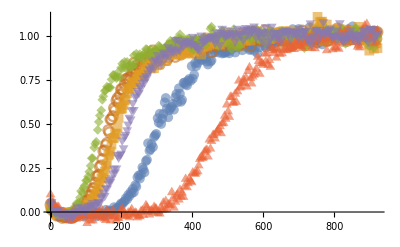

```mathematica
dataplot=ListPlot[{data1with0,data15with0,data2with0,data1with10,data15with10,data2with10},PlotMarkers->{Automatic,10},PlotStyle->Opacity[0.6]]
```

#### Raw data

```mathematica
rawdata1with0=Import["Input_files/AB42_raw_data/data_varyingAB_0D.tsv",{"Data",All,{1,2}}];
rawdata1with0=Delete[rawdata1with0,1];
rawdata15with0=Import["Input_files/AB42_raw_data/data_varyingAB_0D.tsv",{"Data",All,{3,4}}];
rawdata15with0=Delete[rawdata15with0,1];
rawdata2with0=Import["Input_files/AB42_raw_data/data_varyingAB_0D.tsv",{"Data",All,{5,6}}];
rawdata2with0=Delete[rawdata2with0,1];
rawdata1with10=Import["Input_files/AB42_raw_data/data_varyingAB_10D.tsv",{"Data",All,{1,2}}];
rawdata1with10=Delete[rawdata1with10,1];
rawdata15with10=Import["Input_files/AB42_raw_data/data_varyingAB_10D.tsv",{"Data",All,{3,4}}];
rawdata15with10=Delete[rawdata15with10,1];
rawdata2with10=Import["Input_files/AB42_raw_data/data_varyingAB_10D.tsv",{"Data",All,{5,6}}];
rawdata2with10=Delete[rawdata2with10,1];
```

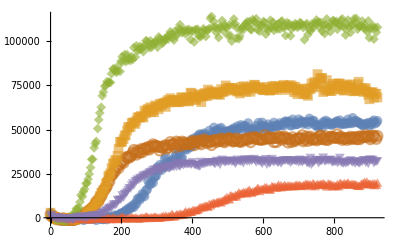

```mathematica
dataplot=ListPlot[{rawdata1with0,rawdata15with0,rawdata2with0,rawdata1with10,rawdata15with10,rawdata2with10},PlotMarkers->{Automatic,10},PlotStyle->Opacity[0.6]]
```

#### Normalisations (from amylofit)

```mathematica
lmax=Length[rawdata1with0]-1;
l=23;
norm10=1/(l+1)*Sum[rawdata1with0[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata15with0]-1;
l=48;
norm150=1/(l+1)*Sum[rawdata15with0[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata2with0]-1;
l=47;
norm20=1/(l+1)*Sum[rawdata2with0[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata6]-1;
l=22;
norm6=1/(l+1)*Sum[rawdata6[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata1with10]-1;
l=31;
norm110=1/(l+1)*Sum[rawdata1with10[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata15with10]-1;
l=10;
norm1510=1/(l+1)*Sum[rawdata15with10[[n]][[2]],{n,lmax-l,lmax}]

lmax=Length[rawdata2with10];
l=1;
norm210=1/(l+1)*Sum[rawdata2with10[[n]][[2]],{n,lmax-l,lmax}]
```

53759.1

73374.

108657.

27125.2

19209.1

31986.4

45539.

## Prediction based on global fit

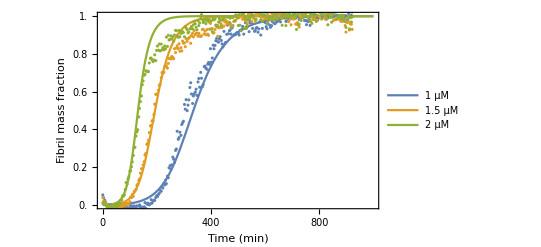

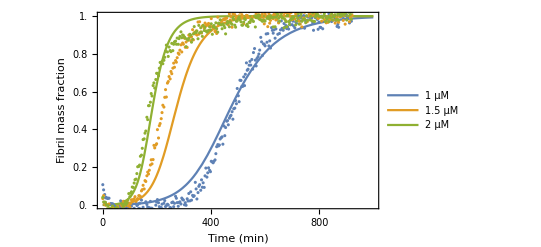

```mathematica
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)
Keq=1/(40*10^(-6));
i01=10.*10^(-6);
ξ1=1/(1+Keq*i01);


(*Plot solutions*)

Show[Plot[{Mass[t,λ,κ],Mass[t,λ*(1.5)^(nc/2),κ*(1.5)^((n2+1)/2)],Mass[t,λ*(2)^(nc/2),κ*(2)^((n2+1)/2)]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}},PlotLegends->LineLegend[{"1 μM","1.5 μM","2 μM"}]],ListPlot[{data1with0,data15with0,data2with0}]]

Show[Plot[{Mass[t,λ*ξ1^((nc+1)/2),κ*ξ1^((n2+1)/2)],Mass[t,λ*(1.5)^(nc/2)*ξ1^((nc+1)/2),κ*(1.5)^((n2+1)/2)*ξ1^((n2+1)/2)],Mass[t,λ*(2)^(nc/2)*ξ1^((nc+1)/2),κ*(2)^((n2+1)/2)*ξ1^((n2+1)/2)]},{t,0,1000},PlotRange->{All,{0,1}},PlotStyle->{Thick},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,1,0.2],None},{Range[0,1000,200],None}},PlotLegends->LineLegend[{"1 μM","1.5 μM","2 μM"}]],ListPlot[{data1with10,data15with10,data2with10}]]
```

#### Export data as xls

```mathematica
m0=Table[Mass[t,λ*ξ1^((nc+1)/2),κ*ξ1^((n2+1)/2)],{t,1000}];
m0//TableForm;

m1=Table[Mass[t,λ*(1.5)^(nc/2)*ξ1^((nc+1)/2),κ*(1.5)^((n2+1)/2)*ξ1^((n2+1)/2)],{t,1000}];
m1//TableForm;

m2=Table[Mass[t,λ*(2)^(nc/2)*ξ1^((nc+1)/2),κ*(2)^((n2+1)/2)*ξ1^((n2+1)/2)],{t,1000}];
m2//TableForm;

Export["Pred1uM10DAb40.xls",m0,"XLS"]
Export["Pred15uM10DAb40.xls",m1,"XLS"]
Export["Pred2uM10DAb40.xls",m2,"XLS"]
```

Pred1uM10DAb40.xls

Pred15uM10DAb40.xls

Pred2uM10DAb40.xls

#### Raw data

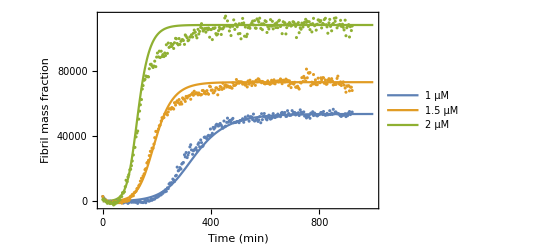

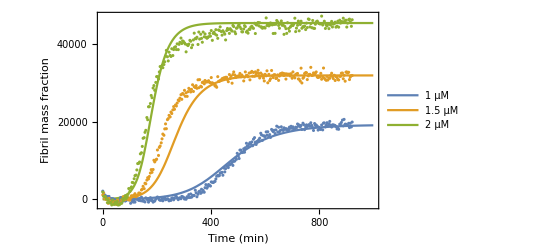

```mathematica
mtot=1.*10^(-6);
kp=3*10^6*60;
kn=1.6*10^(2)*3600/kp;(*5.22*10^5/kp;*)
k2=5.9*10^(10)*3600/kp;(*2.57*10^(14)/kp;*)
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

(* Relevant parameters to be changed: kon, koff, Keq and Keq with fibrils *)

Keqfibrils=92*10^(-9);  (* Equilibrium binding constant to fibrils...in units of concentration...the smaller the stronger bound are the monomers to the fibrils *)
kofffibrils=92*10^(-9)*kp;(**kp*Keqfibrils;*)
Keq=1/(40*10^(-6));
i01=10.*10^(-6);
ξ1=1/(1+Keq*i01);


(*Plot solutions*)

Show[Plot[{norm10*Mass[t,λ,κ],
norm150*Mass[t,λ*(1.5)^(nc/2),κ*(1.5)^((n2+1)/2)],
norm20*Mass[t,λ*(2)^(nc/2),κ*(2)^((n2+1)/2)]},{t,0,1000},PlotRange->{All,All},PlotStyle->{Thick},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,150000,40000],None},{Range[0,1000,200],None}},PlotLegends->LineLegend[{"1 μM","1.5 μM","2 μM"}]],ListPlot[{rawdata1with0,rawdata15with0,rawdata2with0}]]

Show[Plot[{norm110*Mass[t,λ*ξ1^((nc+1)/2),κ*ξ1^((n2+1)/2)],
norm1510*Mass[t,λ*(1.5)^(nc/2)*ξ1^((nc+1)/2),κ*(1.5)^((n2+1)/2)*ξ1^((n2+1)/2)],norm210*Mass[t,λ*(2)^(nc/2)*ξ1^((nc+1)/2),κ*(2)^((n2+1)/2)*ξ1^((n2+1)/2)]},{t,0,1000},PlotRange->{All,All},PlotStyle->{Thick},Axes->False,FrameLabel->{"Time (min)","Fibril mass fraction"},Frame->True,PlotRange->{{0,10},{-0.0,1.05}},FrameStyle->Black,FrameTicks->{{Range[0,80000,10000],None},{Range[0,1000,200],None}},PlotLegends->LineLegend[{"1 μM","1.5 μM","2 μM"}]],ListPlot[{rawdata1with10,rawdata15with10,rawdata2with10}]]
```

#### Export data as xls

```mathematica
m0=Table[{t,norm10*Mass[t,λ,κ],
norm150*Mass[t,λ*(1.5)^(nc/2),κ*(1.5)^((n2+1)/2)],
norm20*Mass[t,λ*(2)^(nc/2),κ*(2)^((n2+1)/2)]},{t,0,1000,1}];
m0//TableForm;

Export["Fit_varyingAb42_0D_raw.xls",m0,"XLS"]
```

Fit_varyingAb42_0D_raw.xls

```mathematica
m0=Table[{t,norm110*Mass[t,λ*ξ1^((nc+1)/2),κ*ξ1^((n2+1)/2)],
norm1510*Mass[t,λ*(1.5)^(nc/2)*ξ1^((nc+1)/2),κ*(1.5)^((n2+1)/2)*ξ1^((n2+1)/2)],norm210*Mass[t,λ*(2)^(nc/2)*ξ1^((nc+1)/2),κ*(2)^((n2+1)/2)*ξ1^((n2+1)/2)]},{t,0,1000,1}];
m0//TableForm;

Export["Fit_varyingAb42_10D_raw.xls",m0,"XLS"]
```

Fit_varyingAb42_10D_raw.xls